```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/TopEFT-UFO/TopEFT-UFO",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

{A→V(1),Z→V(2),W→V(3),G→V(4),ghA→U(1),ghZ→U(2),ghWp→U(3),ghWm→U(4),ghG→U(5),ve→F(1),vm→F(2),vt→F(3),e→F(4),mu→F(5),ta→F(6),u→F(7),c→F(8),t→F(9),d→F(10),s→F(11),b→F(12),H→S(1),G0→S(2),GluonPropagator→S(3)}

## Top - G - G vertex

generic model {../Models/TopEFT-UFO/TopEFT-UFO_FC} initialized

classes model {../Models/TopEFT-UFO/TopEFT-UFO} initialized

in total: 1 Particles insertion

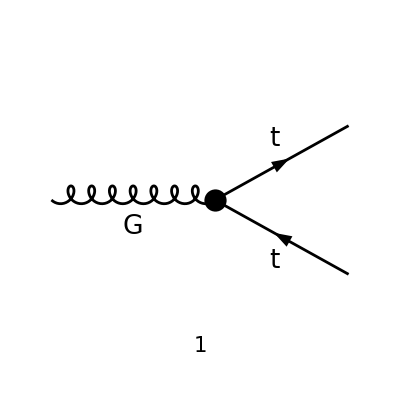

```mathematica
tops = CreateTopologies[0,1->2];
processGGT =  { V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},GenericModel->"../Models/TopEFT-UFO/TopEFT-UFO_FC"];
Paint[allDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},List->False,DropSumOver->True,LorentzIndexNames-> {μ},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 1 Particles amplitude

4 ⅈ π^(5/2) √aS yDM^2 k^μ (C1+C11+C12) (-(γ·p1)).(γ̄)^6 T_Col2Col3^Glu1+4 ⅈ π^(5/2) √aS yDM^2 k^μ (C1+C11+C12) (-(γ·p2)).(γ̄)^6 T_Col2Col3^Glu1-4 ⅈ π^(5/2) √aS yDM^2 p1^μ (C1+C11+C12) (-(γ·p2)).(γ̄)^6 T_Col2Col3^Glu1-4 ⅈ π^(5/2) √aS yDM^2 p2^μ (C1+C11+C12) (-(γ·p1)).(γ̄)^6 T_Col2Col3^Glu1-4 ⅈ π^(5/2) √aS p1^2 yDM^2 γ^μ.(γ̄)^6 (C1+C11+C12) T_Col2Col3^Glu1-4 ⅈ π^(5/2) √aS p2^2 yDM^2 γ^μ.(γ̄)^6 (C1+C11+C12) T_Col2Col3^Glu1-2 ⅈ π^(5/2) √aS k^2 yDM^2 (C1+2 C12) γ^μ.(γ̄)^6 T_Col2Col3^Glu1+2 ⅈ π^(5/2) √aS yDM^2 (C1+2 C12) k^μ (γ·k).(γ̄)^6 T_Col2Col3^Glu1-ⅈ γ^μ.(γ̄)^6 (2 π^2 C00eff GS yDM^2+GS) T_Col2Col3^Glu1-ⅈ GS γ^μ.(γ̄)^7 T_Col2Col3^Glu1

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

-ⅈ T_Col2Col3^Glu1 (γ^μ.(γ̄)^6 (2 π^(5/2) √aS yDM^2 (2 (p1^2+p2^2) (C1+C11+C12)+k^2 (C1+2 C12))+2 π^2 C00eff GS yDM^2+GS)+2 π^(5/2) √aS yDM^2 (2 (C1+C11+C12) ((k^μ-p1^μ) (γ·p2).(γ̄)^6+(k^μ-p2^μ) (γ·p1).(γ̄)^6)-(C1+2 C12) k^μ (γ·k).(γ̄)^6)+GS γ^μ.(γ̄)^7)

```mathematica
ampC=FCReplaceMomenta[ampB,{k->p1+p2}]
```

-ⅈ T_Col2Col3^Glu1 (γ^μ.(γ̄)^6 (2 π^(5/2) √aS yDM^2 ((C1+2 C12) (p1+p2)^2+2 (p1^2+p2^2) (C1+C11+C12))+2 π^2 C00eff GS yDM^2+GS)+2 π^(5/2) √aS yDM^2 (2 (C1+C11+C12) (((p1+p2)^μ-p1^μ) (γ·p2).(γ̄)^6+((p1+p2)^μ-p2^μ) (γ·p1).(γ̄)^6)-(C1+2 C12) (p1+p2)^μ (γ·p1+γ·p2).(γ̄)^6)+GS γ^μ.(γ̄)^7)

```mathematica
ampD = Expand[ExpandScalarProduct[ampC]]
```

-2 ⅈ C00eff GS π^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C1 π^(5/2) (γ·p1).(γ̄)^6 p1^μ T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C11 π^(5/2) (γ·p1).(γ̄)^6 p1^μ T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C12 π^(5/2) (γ·p1).(γ̄)^6 p1^μ T_Col2Col3^Glu1 yDM^2+2 ⅈ √aS C1 π^(5/2) (γ·p1+γ·p2).(γ̄)^6 p1^μ T_Col2Col3^Glu1 yDM^2+4 ⅈ √aS C12 π^(5/2) (γ·p1+γ·p2).(γ̄)^6 p1^μ T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C1 π^(5/2) (γ·p2).(γ̄)^6 p2^μ T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C11 π^(5/2) (γ·p2).(γ̄)^6 p2^μ T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C12 π^(5/2) (γ·p2).(γ̄)^6 p2^μ T_Col2Col3^Glu1 yDM^2+2 ⅈ √aS C1 π^(5/2) (γ·p1+γ·p2).(γ̄)^6 p2^μ T_Col2Col3^Glu1 yDM^2+4 ⅈ √aS C12 π^(5/2) (γ·p1+γ·p2).(γ̄)^6 p2^μ T_Col2Col3^Glu1 yDM^2-6 ⅈ √aS C1 π^(5/2) γ^μ.(γ̄)^6 p1^2 T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C11 π^(5/2) γ^μ.(γ̄)^6 p1^2 T_Col2Col3^Glu1 yDM^2-8 ⅈ √aS C12 π^(5/2) γ^μ.(γ̄)^6 p1^2 T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C1 π^(5/2) γ^μ.(γ̄)^6 (p1·p2) T_Col2Col3^Glu1 yDM^2-8 ⅈ √aS C12 π^(5/2) γ^μ.(γ̄)^6 (p1·p2) T_Col2Col3^Glu1 yDM^2-6 ⅈ √aS C1 π^(5/2) γ^μ.(γ̄)^6 p2^2 T_Col2Col3^Glu1 yDM^2-4 ⅈ √aS C11 π^(5/2) γ^μ.(γ̄)^6 p2^2 T_Col2Col3^Glu1 yDM^2-8 ⅈ √aS C12 π^(5/2) γ^μ.(γ̄)^6 p2^2 T_Col2Col3^Glu1 yDM^2-ⅈ GS γ^μ.(γ̄)^6 T_Col2Col3^Glu1-ⅈ GS γ^μ.(γ̄)^7 T_Col2Col3^Glu1

```mathematica
ampE = Expand[Collect[Simplify[( ampD)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-ⅈ GS γ^μ.(γ̄)^6 T_Col2Col3^Glu1 (2 π^2 C00eff yDM^2+π^2 yDM^2 (p1^2 (3 C1+2 C11+4 C12)+p2^2 (3 C1+2 C11+4 C12)+2 (C1+2 C12) (p1·p2))+1)-ⅈ π^2 GS yDM^2 p1^μ T_Col2Col3^Glu1 (2 (C1+C11+C12) (γ·p1).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6)-ⅈ π^2 GS yDM^2 p2^μ T_Col2Col3^Glu1 (2 (C1+C11+C12) (γ·p2).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6)-ⅈ GS γ^μ.(γ̄)^7 T_Col2Col3^Glu1

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampF=Expand[Collect[ampE,{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[Momentum[p1,D],D],DiracGamma[Momentum[p2,D],D],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-ⅈ GS γ^μ.(γ̄)^6 T_Col2Col3^Glu1 (π^2 yDM^2 (2 C00eff+4 MT^2 (C1+C11+C12)+s (C1+2 C12))+1)-ⅈ π^2 GS yDM^2 p1^μ T_Col2Col3^Glu1 (2 (C1+C11+C12) (γ·p1).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6)-ⅈ π^2 GS yDM^2 p2^μ T_Col2Col3^Glu1 (2 (C1+C11+C12) (γ·p2).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6)-ⅈ GS γ^μ.(γ̄)^7 T_Col2Col3^Glu1

```mathematica
ampF/.{C00eff->C00-2 MT^2(C1+C11+C12)-s/2 (C1+2 C12)}//Simplify
```

-ⅈ GS T_Col2Col3^Glu1 (γ^μ.(γ̄)^7+(2 π^2 C00 yDM^2+1) γ^μ.(γ̄)^6+π^2 yDM^2 p1^μ (2 (C1+C11+C12) (γ·p1).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6)+π^2 yDM^2 p2^μ (2 (C1+C11+C12) (γ·p2).(γ̄)^6-(C1+2 C12) (γ·p1+γ·p2).(γ̄)^6))

```mathematica
Expand[%]
```

-2 ⅈ π^2 C00 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1+ⅈ π^2 C1 GS yDM^2 p1^μ T_Col2Col3^Glu1 (γ·p1+γ·p2).(γ̄)^6+ⅈ π^2 C1 GS yDM^2 p2^μ T_Col2Col3^Glu1 (γ·p1+γ·p2).(γ̄)^6-2 ⅈ π^2 C1 GS yDM^2 p1^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-2 ⅈ π^2 C1 GS yDM^2 p2^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1-2 ⅈ π^2 C11 GS yDM^2 p1^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-2 ⅈ π^2 C11 GS yDM^2 p2^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1+2 ⅈ π^2 C12 GS yDM^2 p1^μ T_Col2Col3^Glu1 (γ·p1+γ·p2).(γ̄)^6+2 ⅈ π^2 C12 GS yDM^2 p2^μ T_Col2Col3^Glu1 (γ·p1+γ·p2).(γ̄)^6-2 ⅈ π^2 C12 GS yDM^2 p1^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-2 ⅈ π^2 C12 GS yDM^2 p2^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1-ⅈ GS γ^μ.(γ̄)^6 T_Col2Col3^Glu1-ⅈ GS γ^μ.(γ̄)^7 T_Col2Col3^Glu1

```mathematica
DiracSimplify[%]
```

-2 ⅈ π^2 C00 GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1+ⅈ π^2 C1 GS yDM^2 p1^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1+ⅈ π^2 C1 GS yDM^2 p2^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-ⅈ π^2 C1 GS yDM^2 p1^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-ⅈ π^2 C1 GS yDM^2 p2^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1-2 ⅈ π^2 C11 GS yDM^2 p1^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-2 ⅈ π^2 C11 GS yDM^2 p2^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1+2 ⅈ π^2 C12 GS yDM^2 p1^μ (γ·p2).(γ̄)^6 T_Col2Col3^Glu1+2 ⅈ π^2 C12 GS yDM^2 p2^μ (γ·p1).(γ̄)^6 T_Col2Col3^Glu1-ⅈ GS γ^μ.(γ̄)^6 T_Col2Col3^Glu1-ⅈ GS γ^μ.(γ̄)^7 T_Col2Col3^Glu1

```mathematica
Expand[Collect[%,{C00eff,C11,C12,C1},foo]]/.foo->FullSimplify
```

-ⅈ GS T_Col2Col3^Glu1 (γ^μ.(γ̄)^7+(2 π^2 C00 yDM^2+1) γ^μ.(γ̄)^6)-ⅈ π^2 C1 GS yDM^2 (p1^μ-p2^μ) T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6)-2 ⅈ π^2 C11 GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p1).(γ̄)^6+p2^μ (γ·p2).(γ̄)^6)+2 ⅈ π^2 C12 GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)

```mathematica
PaVe
```